Solving the Poisson-Fermi-Dirac equation in LiF, Li2O, and Li2CO3
Michael W Swift and James W Swift

Accompanying “Modeling the electrical double layer at solid-state electrochemical interfaces” by Michael W Swift, James W Swift, and Yue Qi

We consider the system

```mathematica
v' = a(f)
f'==v
a(f) = 1/(B ⅇ^-f+1)-1/(B ⅇ^f+1)
```

The asymptotic behavior of f is represented by the fixed point at (0,0) in this system of equations.  Any solution on the stable manifold of this fixed point will have the correct asymptotic behavior.  To do so, we will find a point some small distance ϵ from the fixed point in the stable eigenspace of the fixed point, then evolve backwards in time to find a point that matches the initial condition for f.  We set x=0 at that point, and this gives us the solution.

The Jacobian of this system at the critical point (0,0) is

```mathematica
J = ({{(∂v)/(∂f), (∂v)/(∂v)}, {(∂a)/(∂f), (∂a)/(∂v)}})=({{0, 1}, {(2B)/(1+B)^2, 0}})
```

The stable eigenspace is spanned by the eigenvector

```mathematica
V=({{(B+1)/B}, {-√(2/B)}})  , J V = ({{-√(2/B)}, {2/(B+1)}})  = (-√(2B))/(B+1)V
```

We therefore take V*ϵ as the starting point for some small ϵ.  Save V as eigen below:

```mathematica
eqn=f''[x]==1/(B*ⅇ^(-f[x])+1)-1/(B*ⅇ^f[x]+1);
```

```mathematica
a[f_,B_]:=1/(B*ⅇ^-f+1)-1/(B*ⅇ^f+1);
```

```mathematica
eigen={(B+1)/B,-(√2)/(√B)};
```

```mathematica
asymptoticSolution[eqn_,eigen_,BIn_,f0_]:=Module[{eps,xEvec,xMax,unstableManifold,xSol},
eps = 1/100;
xEvec = 10^10; (* large:  This is the value of x where we impose that the solution is close to the fixed point at the origin, in the direction of the stable eigenvector *)
xMax =xEvec + 10; (* xMax ≥ xEvec.  This can be used so see the solution divierge to infinity or -infinity *)
unstableManifold= Part[NDSolve[{eqn/.B->BIn,
 f[xEvec]== eps*eigen[[1]]/.B->BIn, f'[xEvec]==eps*eigen[[2]]/.B->BIn},f, {x,0,xMax}], 1];
(* Solve backwards in time starting from eps*eigen *)  
(* Take the first and only solution *)
xSol=Part[FindRoot[f[x0]==f0/.unstableManifold,{x0,3.5*10^9},AccuracyGoal->5,PrecisionGoal->5],1];
(* Find x0 corresponding to f0 *)
{unstableManifold,x0/.xSol,xEvec}
(* Return replacement rule for the solution, x0, and xEvec *)];
```

```mathematica
U[f_, B_] :=  -Log[ (Exp[f] + B)/(1+B)] +-Log[ (Exp[-f] + B)/(1+B)];
p0[f0_,B_]:=Sqrt[-2*U[f0,B]];
f0Prime[f_,B_]:=-Sqrt[-2*U[f, B ] ];
cVal = 0;  (* for purists, who like the straight line on the log-linear graph, even though the fit is not good.  Not for engineers! *)
cVal = 6.74;  (* setting f_2(xi_1) = numerical value. The fit looks perfect! Maybe too good! *) 
cVal = 7.39; (* seting f_2(xi_1) = f_1(xi_1). *)
(* the last line defines c to the the value actually used *)
fa[x_,f0_,B_]:=-2Log[(x-cVal)/Sqrt[2 B]];  (* The logarithmic approximation to f_2.  Not used in the figures *)
(*JWS: the old f_3 from the paper *)
fExp[f0_,B_,x_]:=4*Exp[-x/Sqrt[B/2]]; (* The exponential approximation to f_2 *)
fExp[f0_,B_,x_]:=4 ArcTanh[Exp[-(x-cVal)/Sqrt[B/2]]]; (*f_2 This is defined last because it's the one we actually use.  *)
```

```mathematica
(* Physical constants *)
e=Quantity[1,"electron charge"];
k=Quantity[1,"BoltzmannConstant"];
T=Quantity[300,"K"];
ϵ0=Quantity[1,"ϵ0"];
```

```mathematica
(*(* LiF quantities: input *)
(* Uncomment desired material data and re-run all cells *)
materialName="LiF";
ϵr=9.0; (* Dielectric constant *)
ϕ0=Quantity[-1.9160630915364418,"Volts"]; (* Potential offset *)
NSites=UnitConvert[32 / Quantity[8.116767673775174, "Angstroms"]^3,"cm^-3"]; (* Density of defect sites *)
Eform=Quantity[0.9733510180664657,"eV"]; (* Defect formation energy at charge neutrality *)
α = 0.1;(* Saturation factor *)*)
```

```mathematica
(* Materials properties: input *)
materialName="Li2O";
ϵr=7.27; (* Dielectric constant *)
ϕ0=Quantity[-2.183321390809776,"Volts"]; (* Potential offset with electrode*)
NSites= Quantity[0.08081057052972979, "Angstroms^-3"]; (* Density of defect sites *)
Eform=Quantity[0.8601251285608837,"eV"]; (* Defect formation energy at charge neutrality *)
α = 0.1;(* Saturation factor *)
```

```mathematica
(*(* Materials properties: input *)
materialName="Li2O_110";
ϵr=7.27; (* Dielectric constant *)
ϕ0=Quantity[-0.7104936557674408,"Volts"]; (* Potential offset with electrode*)
NSites= Quantity[0.08081057052972979, "Angstroms^-3"]; (* Density of defect sites *)
Eform=Quantity[0.8601251285608837,"eV"]; (* Defect formation energy at charge neutrality *)
α = 0.1;(* Saturation factor *)*)
```

```mathematica
(*materialName="Li2CO3";
ϵr=5.64; (* Dielectric constant *)
ϕ0=Quantity[-1.844417907251016,"Volts"]; (* Potential offset with electrode*)
NSites= Quantity[0.016494078801107086, "Angstroms^-3"]; (* Density of defect sites *)
Eform=Quantity[0.9110166485045346,"eV"]; (* Defect formation energy at charge neutrality *)
α = 0.1;(* Saturation factor *)
*)
```

JWS gets a beep with this next cell.  It might be my version of Mathematica (11.1.1.0).

```mathematica
(* Derived quantities *)
ftoV = QuantityMagnitude[UnitConvert[k*T/e,"Volts"]];
BIn=SetPrecision[α*Exp[Eform/(k*T)],100];
λ=SetPrecision[QuantityMagnitude[UnitConvert[√((ϵr ϵ0 k T)/(α*NSites e^2)),"Angstroms"]],100];
f0=SetPrecision[-(e ϕ0)/(k T),100];
ϕ0mag=QuantityMagnitude[ϕ0];

(* Solve it *)
{sol,x0,xEvec}=asymptoticSolution[eqn,eigen,BIn,f0];

(* Dimensionless parts *)
fp0=f0Prime[f0,BIn];
fp0Numerical=f'[x0]/.sol;
quadraticPiece[x_]:=f0+fp0*x+1/2x^2;
logarithmicPiece[x_]:=fa[x,f0,BIn];
exponentialPiece[x_]:=fExp[f0,BIn,x];

(* Return dimensions *)
ϕ[x_]:=-ϕ0mag-ftoV*f[x/λ+x0]/.sol;
ϕ1[x_]:=-ϕ0mag-ftoV*quadraticPiece[x/λ];
(*ϕ2[x_]:=-ϕ0mag-ftoV*logarithmicPiece[x/λ];*)
ϕ2[x_]:=-ϕ0mag-ftoV*exponentialPiece[x/λ];

Print[materialName]

Print["For tab:PFD_params"]
Print[StringForm["f0 = ``, f'0 = `` (Numerical solution has f'0 = ``), λ = `` Å, B = ``",NumberForm[f0,4],NumberForm[fp0,4],NumberForm[fp0Numerical,4] ,NumberForm[λ,3], NumberForm[BIn,4] ]]
Print[];

ξ1=-fp0;x1=ξ1*λ;
Print["ξ1 = ", ξ1];
Print["approximate c = ", ξ1 -1/Sqrt[2]];
(* JWS: This was the original: ξ2=Sqrt[BIn]/2;x2=ξ2*λ; *)
ξ2=Sqrt[BIn/2];x2=ξ2*λ;

surfaceCharge=UnitConvert[Sqrt[α*NSites*k*T*ϵ0/ϵr]*fp0, "electron charge/nm^2"];

Print["For tab:crossover_thicknesses"]
Print[StringForm["x1 = `` Å, ϕ(x1) = `` V, x2 = `` Å, ϕ(x2) = `` V, ϕ(∞) = `` V, σ Li = ``",
NumberForm[x1,3], NumberForm[ϕ[x1],3],NumberForm[x2,3], NumberForm[ϕ[x2],3],NumberForm[-ϕ0mag,3],NumberForm[surfaceCharge,3]]]
Print[];

capacitance=UnitConvert[surfaceCharge/ϕ0,"microFarad / cm^2"]

Δϕ=1.24000;
xStarLiPON=x/.FindRoot[ϕ[x]==Δϕ,{x,10},AccuracyGoal->3, PrecisionGoal->3];

Δϕ=1.62000;
xStarLLZO=x/.FindRoot[ϕ[x]==Δϕ,{x,10},AccuracyGoal->3, PrecisionGoal->3];


Print["For tab:design"]
Print[StringForm["x* LiPON = `` Å, x* LLZO = `` Å ",NumberForm[xStarLiPON,3],NumberForm[xStarLLZO,3]]]


(*(* Export EDL data *)
data=Table[{x,ϕ[x]},{x,0,xStarLiPON,xStarLiPON/50}];
Export[NotebookDirectory[]<>materialName<>"_EDL_data.txt",data, "Table"];*)
```

Li2O

For tab:PFD_params

f0 = 84.45, f'0 = -10.34 (Numerical solution has f'0 = -10.34), λ = 0.359 Å, B = 2.815×10^13

ξ1 = 10.34273675308194254225248004293057033489544211718116167822723943414347756344020389339292650961330488

approximate c = 9.63562997189539501785163568082572129561060617949268764163889956514811132420915037396773274244948409

For tab:crossover_thicknesses

x1 = 3.71 Å, ϕ(x1) = 1.4 V, x2 = 1.34×10^6 Å, ϕ(x2) = 2.14 V, ϕ(∞) = 2.18 V, σ Li = -0.412

3.02455 µF/cm^2

For tab:design

x* LiPON = 2.52 Å, x* LLZO = 52.9 Å

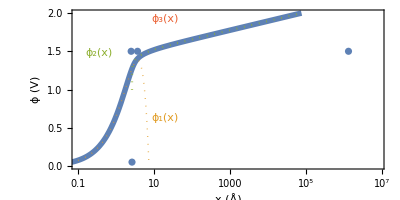

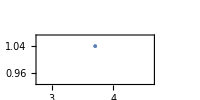

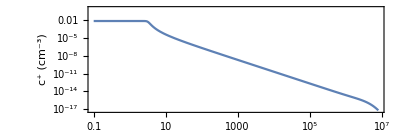

```mathematica
(* Make plots *)
xMax=(xEvec-x0)*λ;mainPlot=Show[
LogLinearPlot[{ϕ[x],ϕ1[x],ϕ2[x],-ϕ0mag},{x,0.001,xMax},FrameStyle->Directive[14,Black],AspectRatio->1/2,PlotRange->{{0.1,xMax},{0,2.0}},FrameLabel->{"x (Å)","ϕ (V)"},PlotStyle->{Thickness[0.01],{Thick,Dotted},Dotted,{Thin,Black}},Frame->True, Epilog->{
Text[Style["ϕ_1(x)",{Medium,ColorData[97,2]}], {3,-ϕ0mag-ftoV*60}],
Text[Style["ϕ_2(x)",{Medium,ColorData[97,3]}], {-1,-ϕ0mag-0.7}],
Text[Style["ϕ_3(x)",{Medium,ColorData[97,4]}], {3,-ϕ0mag-ftoV*10}]}],
ListLogLinearPlot[{{x1,1.5},{xStarLiPON,1.5},{x2,1.5},{cVal*λ,0.05}}]]

insetPlot=Show[
Plot[{ϕ[x], ϕ1[x], ϕ2[x]}, {x, .75x1, 1.25x1}, PlotRange -> {.93, 1.07},FrameStyle->Directive[14,Black],AspectRatio->1/2,FrameLabel->{"x (Å)","ϕ (V)"},ImageSize->200,PlotStyle->{Thickness[0.02],{Thick,Dotted},{Thickness[0.015],Dotted},{Thickness[0.015],Dotted}, {Thin,Black}},Frame->True, Epilog->{
Text[Style["ϕ_2(x)",{Medium,ColorData[97,3]}], {3,1.94}],
Text[Style["ϕ_3(x)",{Medium,ColorData[97,4]}], {5,1.88}]}],
ListPlot[{{x1,1.04}}]]

conc[x_]:=QuantityMagnitude[NSites]*α*a[(f[x/λ+x0])/.sol,BIn];

concPlot=LogLogPlot[conc[x],{x,0.1,xMax},Frame->True,PlotRange->{{0.1,xMax},Automatic},FrameStyle->Directive[14,Black],AspectRatio->1/3,FrameLabel->{"x (Å)","c^+ (cm^-3)"}]
```

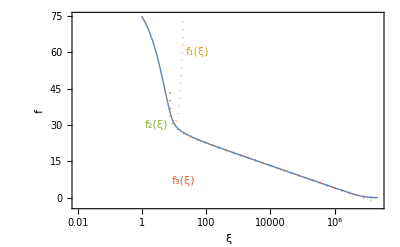

```mathematica
(* Dimensionless plot *)
dimensionlessPlot = LogLinearPlot[{f[x+x0]/.sol,quadraticPiece[x],logarithmicPiece[x],exponentialPiece[x]},{x,0.0001,xEvec-x0},FrameStyle->Directive[14,Black],PlotRange->{{0.01,xEvec-x0},{-3,75}},FrameLabel->{ξ,f},PlotStyle->{Thick,{Thick,Dotted},Dotted,Dotted},Frame->True, Epilog->{
Text[Style["f_1(ξ)",{Medium,ColorData[97,2]}], {4,60}],
Text[Style["f_2(ξ)",{Medium,ColorData[97,3]}], {1,30}],
Text[Style["f_3(ξ)",{Medium,ColorData[97,4]}], {3,7}]}]
```

This numerical investigation was done before we found the prefactor of 4 in the exponential decay regime.

```mathematica
E * N@f[ξ2+x0]/.sol
E^2 N@f[2 ξ2+x0]/.sol
E^3 N@f[3 ξ2+x0]/.sol
E^4 N@f[4 ξ2+x0]/.sol
```

4.19669

4.02469

4.00331

4.00045

Here are the numerics to justify statements after equation (19).   We get the 0.04% and the 0.6% here, and the 10^-4% in the next cell.

```mathematica
numApprox = N@f[10 ξ1 + x0]/.sol
f2Approx = 4. ArcTanh[Exp[-(10 ξ1-cVal)/ξ2]]
f2ApproxNoC = 4. ArcTanh[Exp[-(10 ξ1)/ξ2]]
(numApprox-f2Approx)/numApprox *100
(numApprox-f2ApproxNoC)/numApprox *100
```

22.5556

22.5322

22.3839

0.103729

0.761057

```mathematica
numApprox = N@f[ξ2+x0]/.sol
f2Approx = 4. ArcTanh[1/E]
(numApprox-f2Approx)/numApprox *100
```

1.54388

1.54387

0.000112091

Print out numbers for use in the python script and/or comparison to intermediate results

```mathematica
QuantityMagnitude[UnitConvert[NSites,"cm^-3"]]
```

8.08106×10^22

```mathematica
UnitConvert[1.0*k,"eV/Kelvin"]
```

0.0000861733 eV/K

```mathematica
UnitConvert[√((ϵ0 k*Quantity[1,"Kelvin"])/(Quantity[1,"cm^-3"] e^2)),"Angstroms"]
```

6.90089807×10^8 Å

```mathematica
UnitConvert[Sqrt[Quantity[1,"cm^-3"]*k*Quantity[1,"Kelvin"]*ϵ0], "electron charge/nm^2"]
```

6.90089807×10^-14 e/nm^2

```mathematica
UnitConvert[Quantity[1.0,"electron charge * nm^-2"]/Quantity[1,"V"],"microFarad / cm^2"]
```

16.0218 µF/cm^2

```mathematica
f0
```

74.11662955922639639538829214870929718017578125

```mathematica
BIn
```

2.24686730695225925×10^15

```mathematica
U[f0,BIn]
```

-38.7683162262820261647151928849993610324678122007760703544909295554260300461717688657874322166638498

```mathematica
fp0
```

-8.805488768521827620662867087329413589422987015237031491497735745709312175676367484023942882919433273

```mathematica
ϕ[x1]
```

1.02176